```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[mb2_,q_,T_]:=1/Exp[(√(q^2+mb2))/T-1];
nbd1x[mb2_,q_,T_]:=-1/T nb[mb2,q,T](nb[mb2,q,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
Epi[q_,mp2_]:=(*√(-0.1 q^2+0.01 q^4+mp2)*)√(q^2+mp2);
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B2thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (-(1+nb[mp2,q,T])/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))+nbd1x[mp2,q,T]/(2 Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))-nb[mp2,q,T]/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))+nbd1x[mp2,q,T]/(2 Epi[q,mp2]^2 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))-nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q,mp2]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2)^2)-(-1+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q,mp2]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((1+nb[mp2,q,T]) (-Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2)^2)-(nb[mp2,q,T] (Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2)^2));
Zpsi[mp2_,mf2_,h_,p0_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(3 π^2)NIntegrate[q^4 Re[F1B2thr[mp2,mf2,p0,q,T,mu]],{q,0,1000}]+1
```

```mathematica
fpidata=Flatten[Import["../renormal/M300.dat"]];
mp2data=Flatten[Import["../mpionmu0.dat"]];
```

```mathematica
data=Table[Zpsi[mp2data[[T]],mf2[6.5,fpidata[[T]]/2],6.5,π T,T,0],{T,1,300}];
```

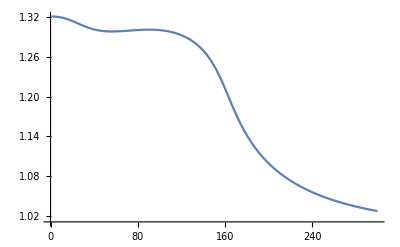

```mathematica
ListLinePlot[data,PlotRange->All]
```

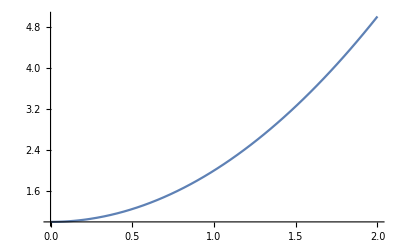

```mathematica
Plot[q^2+0. q^4+1^2,{q,0,2}]
```

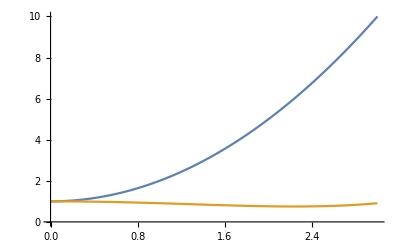

```mathematica
Plot[{p^2+1,-0.1 p^2+0.01 p^4+1},{p,0,3}]
```